```mathematica
G[k_,l_]:=(k+l-1.7)^2+(1.5*k+l-2.9)^2+(2*k+l-3.9)^2+(2.5*k+l-4.5)^2+(3*k+l-6.2)^2
```

```mathematica
Plot3D[G[k,l],{k,-10,10},{l,-10,10}]
```

-Graphics3D-

```mathematica
D[G[k,l],k]
```

2 (-1.7+k+l)+3. (-2.9+1.5 k+l)+4 (-3.9+2 k+l)+5. (-4.5+2.5 k+l)+6 (-6.2+3 k+l)

```mathematica
D[G[k,l],l]
```

2 (-1.7+k+l)+2 (-2.9+1.5 k+l)+2 (-3.9+2 k+l)+2 (-4.5+2.5 k+l)+2 (-6.2+3 k+l)

```mathematica
Solve[{2 (-1.7+k+l)+3. (-2.9+1.5 k+l)+4 (-3.9+2 k+l)+5. (-4.5+2.5 k+l)+6 (-6.2+3 k+l)==0,2 (-1.7+k+l)+2 (-2.9+1.5 k+l)+2 (-3.9+2 k+l)+2 (-4.5+2.5 k+l)+2 (-6.2+3 k+l)==0},{k,l}]
```

{{k→2.12,l→-0.4}}

```mathematica
data={{1,1.7},{1.5,2.9},{2,3.9},{2.5,4.5},{3,6.2}};
```

General::spell1: スペル間違いの可能性があります．新規シンボル"data"はすでにあるシンボル"ata"に似ています．

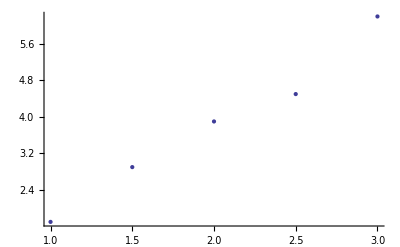

```mathematica
ListPlot[data]
```

```mathematica
Fit[data,{1,k},k]
```

-0.4+2.12 k